# Plotting the Characteristics for First Order PDE:

```mathematica
Q.1  Subscript[u, y] + Subscript[xu, x] ==0
```

```mathematica
char1=D[x[s],s]==x[s]
char2=D[y[s],s]==1
char3=D[u[s],s]==0
sol1=DSolve[{char1,char2,char3},{x[s],y[s],u[s]},s]
```

x'[s]==x[s]

y'[s]==1

u'[s]==0

{{x[s]→ⅇ^s C[1],y[s]→s+C[2],u[s]→C[3]}}

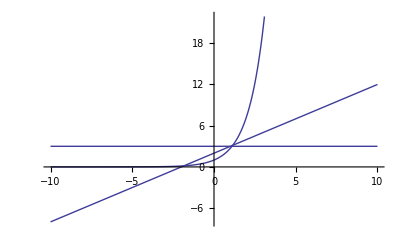

```mathematica
Plot[{x[s],y[s],u[s]}/.sol1/.{C[1]->1,C[2]->2,C[3]->3},{s,-10,10}]
```

```mathematica
Q.2  Subscript[u, x] + Subscript[u, y] ==Sin[x[s]]
```

```mathematica
char1=D[x[s],s]==1
char2=D[y[s],s]==1
char3=D[u[s],s]==Sin[x[s]]
```

x'[s]==1

y'[s]==1

u'[s]==Sin[x[s]]

```mathematica
sol2=DSolve[{char1,char2,char3},{x[s],y[s],u[s]},s]
```

{{x[s]→s+C[1],u[s]→C[2]-Cos[s] Cos[C[1]]+Sin[s] Sin[C[1]],y[s]→s+C[3]}}

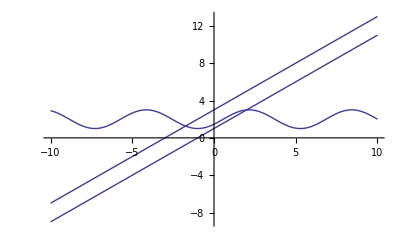

```mathematica
Plot[{x[s],y[s],u[s]}/.sol2/.{C[1]->1,C[2]->2,C[3]->3},{s,-10,10}]
```